# “Równanie Hamiltona-Jacobbiego”

```mathematica
ClearAll["Global `*"];  (* czyszczenie jądra programu ze wszystkich zmiennych *)
```

### Wstęp filozoficzny

mechanika Newtona: m (d^2 r)/dt^2=F(r,t) - druga zasada dynamiki Newtona
mechanika Lagrange’a: L=T-V, równania Eulera-Lagrange’a, równania różniczkowe drugiego rzędu dla położeń i prędkości
mechanika Hamiltona: H=T+V, równiania różniczkowe pierszego rzędu - równania Hamiltona dla położeń i pędów
równanie Hamiltona-Jacobbiego: ∂_t S+H(q_i,p_i→ ∂_q_i S)=0
równania różniczkowe cząstkowe rozwiązujemy metodą separacji zmiennych
relatywistyczne równanie Hamiltona-Jacobbiego: g^αβ∂_α S∂_β S=m

### Równanie Hamiltona - Jacobbiego dla cząstki swobodnej

cząstka swobodna: H=p^2/2m
H-J: ∂_t S+1/2m (∂_x S)^2=0
separacja zmiennych: S=a(t)+S_1(x)
∂_t S=ȧ(t), ∂_x S=S_1'(x)
ȧ(t)+1/2m S_1'(x)^2=0 -> ȧ(t)=-1/2m S_1'(x)^2=-E
a(t)=-Et
1/2m S_1'(x)^2=E
S_1'(x)=-^+√(2mE)x
można sprawdzić, że odtwrzamy równania ruchu klasycznej dynamiki

### Ruch satelity w polu grawitacyjnym Słońca

#### Parametry symulacji

```mathematica
m=0.5; (* masa satelity *)
r0=1; (* punkt startowy na orbicie *)
α=1; (* parametr potencjału V=-α/r *)
e=-0.5; (* energia kinetyczna + potencjalna *)
j0=0.5; (* moment pędu satelity na orbicie *)
```

### Szukanie peryhelium i aphelium orbity

```mathematica
f[r_,j_]:=2m(e+α/r)-j^2/( r^2) (* wyrażenie określające dopuszczalne wartości momentu pędu J i położenia r *)
rob=f[r,j0]r^2; (* pomocniczy wielomian do wyszukania miejsc zerowych wyrażenia f[r,J] dla J=0.3 *)
rmin=NSolve[rob==0][[2,1,2]] ;(* peryhelium *)
rmax=NSolve[rob==0][[1,1,2]]; (* aphelium *)
r0=rmin+0.000001; (* punkt początkowy do rozwiązywania równania różniczkowego *)
```

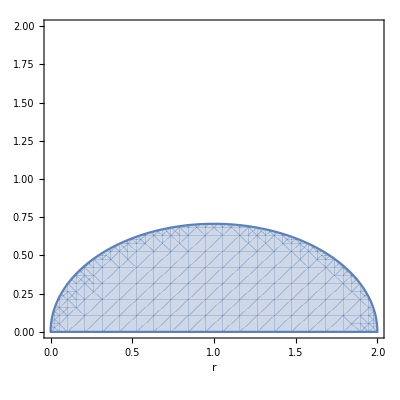

```mathematica
RegionPlot[f[r,j]≥0,{r,0,2},{j,0,2},AxesLabel->{"r"}] (* dopuszczalny zakres parametrów {r,J} *)
```

### Orbita satelity krążącego wokół Słońca

```mathematica
rozw=NDSolve[{phi'[r]==-D[Sqrt[2m(e+α/r)-j^2/( r^2)],j],phi[rmin+0.000001]==0}/.j->j0,phi[r],{r,rmin,rmax}]; (* równanie różniczkowe na ϕ(r) powstałe z obliczeń wykonywanych dla równania Hamiltona-Jacobbiego*)
```

Power::infy: Infinite expression 1/√0. encountered.

NDSolve::nlnum: The function value {ComplexInfinity} is not a list of numbers with dimensions {1} at {r, phi[r]} = {0.292893, -0.00406021}.

NDSolve::ndsz: At r == 1.70711, step size is effectively zero; singularity or stiff system suspected.

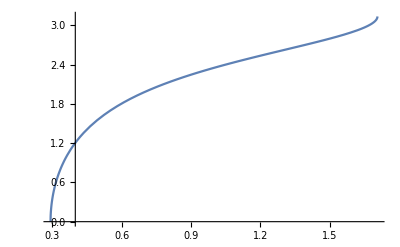

```mathematica
Plot[phi[r]/.rozw,{r,rmin,rmax},ImageSize->400] (* wykres zależności ϕ(r) *)
```

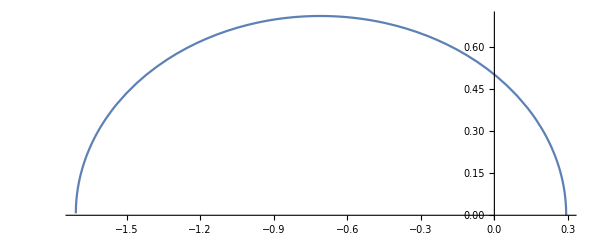

```mathematica
r1=ParametricPlot[{r Cos[phi[r]],r Sin[phi[r]]}/.rozw,{r,rmin,rmax},ImageSize->600] (* wykres parametryczny {x,y}={rcosϕ(r),rsinϕ(r)} *)
```

### Druga część orbity

Power::infy: Infinite expression 1/√0. encountered.

NDSolve::nlnum: The function value {ComplexInfinity} is not a list of numbers with dimensions {1} at {r, phi[r]} = {0.292893, 0.00406021}.

NDSolve::ndsz: At r == 1.70711, step size is effectively zero; singularity or stiff system suspected.

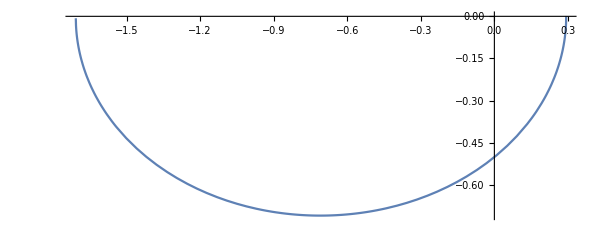

```mathematica
rozw2=NDSolve[{phi'[r]==D[Sqrt[2m(e+α/r)-j^2/( r^2)],j],phi[rmin+0.000001]==0}/.j->j0,phi[r],{r,rmax,rmin}]; (* przeciwny znak w równaniu różniczkowym *)
r2=ParametricPlot[{r Cos[phi[r]],r Sin[phi[r]]}/.rozw2,{r,rmax,rmin},ImageSize->600] (* druga połowa orbity, odwrócone warunki początkowe *)
```

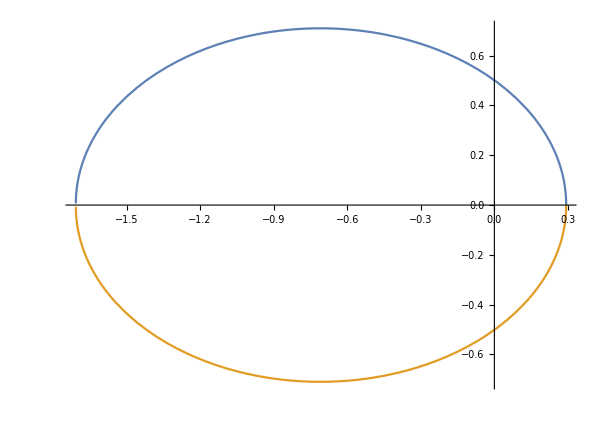

```mathematica
ParametricPlot[{{{r Cos[phi[r]],r Sin[phi[r]]}/.rozw},{{r Cos[phi[r]],r Sin[phi[r]]}/.rozw2}},{r,rmax,rmin},ImageSize->600] (* cała ortita *)
```

## Metryka Schwarzschilda dla fotonu

### Równanie Hamiltona-Jacobbiego

```mathematica
wyr=ee^2/(1-1/r)-(1-1/r)dSr^2-jj^2/r^2-m^2;(* równanie Hamiltona-Jacobbiego *)
sol=NSolve[wyr==0,dSr][[2,1,2]];(* dodatni pierwiastek równania H-J *)
dphidr=D[sol,jj];  (* wyrażenie na pochodną dϕ/dr=Subscript[dS, 1]/dJ *)
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

### Parametry symulacji

```mathematica
r0=5; (* punkt startowy, odległość od środka czarnej dziury*)
mm0=0; (* masa cząstki próbnej, zerowa dla fotonu *)
jj0=0.8; (* moment pędu cząstki *)
ee0=-0.5;(* całkowita energia cząstki *)
```

### Tor ruchu fotonu w pobliżu czarnej dziury

Power::infy: Infinite expression 1/√0. encountered.

NDSolve::nlnum: The function value {ComplexInfinity} is not a list of numbers with dimensions {1} at {r, phi[r]} = {1., 2.56368}.

InterpolatingFunction::dmval: Input value {0.000112041} lies outside the range of data in the interpolating function. Extrapolation will be used.

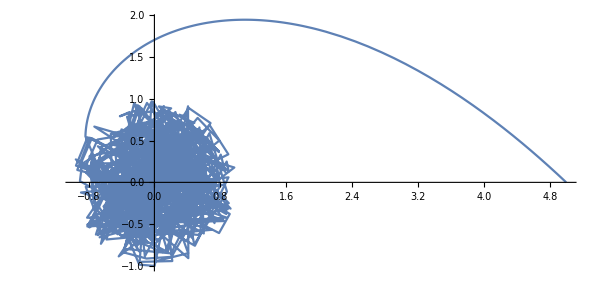

```mathematica
dphidr=dphidr/.{mm->mm0,ee->ee0,jj->jj0}; (* podstawienie wartości liczbowych do rozwiązania *)
rozw1=NDSolve[{phi'[r]==dphidr,phi[r0]==0},phi[r],{r,r0,10^(-5)}]; (* wyznaczenie toru ruchu *)
ParametricPlot[{r Cos[phi[r]],r Sin[phi[r]]}/.rozw1,{r,r0,10^(-5)},ImageSize->600] (* trajektoria fotonu spadającego swobodnie na czarną dziurę *)
```